```mathematica
actual=0.0
target=100.0
filter=Table[{i, actual=(15*actual+target)/16;actual},{i,0,499}];
```

0.

100.

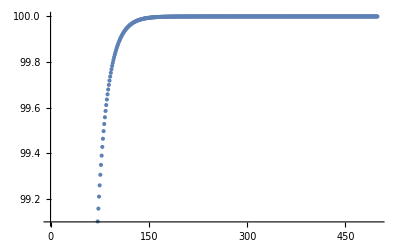

```mathematica
ListPlot[filter]
```

```mathematica
actual=0.0
target=100.0
filter2=Table[{i, actual+=(target-actual)/16;actual},{i,0,499}];
```

0.

100.

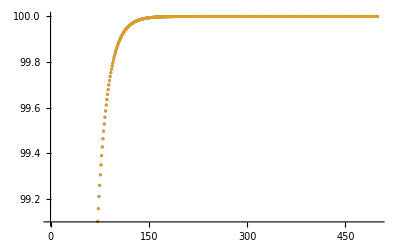

```mathematica
ListPlot[{filter, filter2}]
```